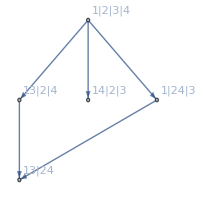

```mathematica
FormulaGraph[ Fold[Plus,FindFullFormula[Graph[{1<->2,2<->3,3<->4}],Table[{i},{i,4}]]]]
```

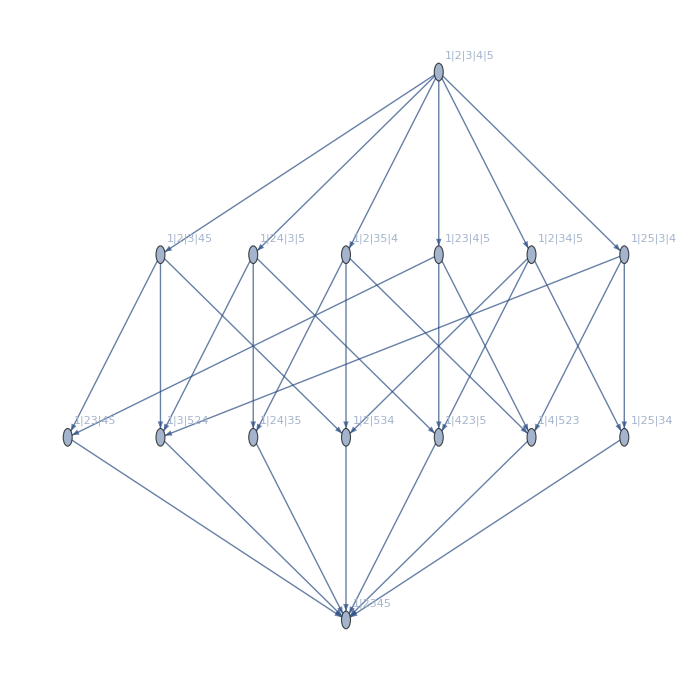

```mathematica
FormulaGraph[ Fold[Plus,FindFullFormula[Graph[{1<->2,1<->3,1<->4,1<->5}],Table[{i},{i,5}]]]]
```

## Looking at the claw

```mathematica
Mingle[c1_,c2_]:=RGBColor[Mean[{c1[[1]],c2[[1]]}],Mean[{c1[[2]],c2[[2]]}],Mean[{c1[[3]],c2[[3]]}]]
```

```mathematica
Mingle2[c1_,c2_]:=RGBColor[Total[{c1[[1]],c2[[1]]}],Total[{c1[[2]],c2[[2]]}],Total[{c1[[3]],c2[[3]]}]]
```

```mathematica
g1=DeleteDuplicates[Traverse[{{1,2},{3},{4},{5}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,3},{2},{4},{5}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{1,4},{2},{3},{5}}]];
```

```mathematica
g4=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4}}]];
```

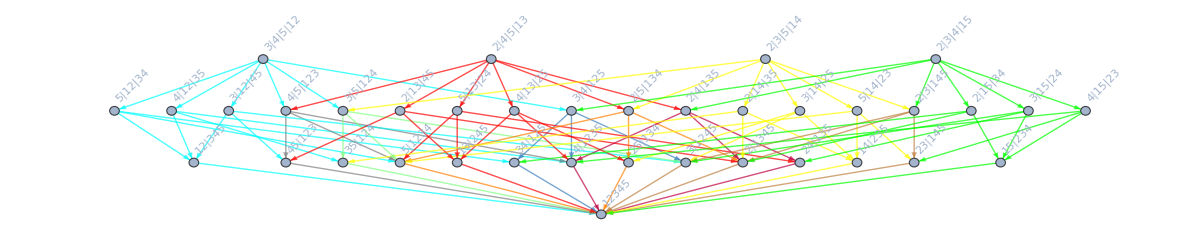

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3,g4]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->Rotate[SymbolToLabel[ SetsToSymbol[#]],Pi/4]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3,g4]]]]],
EdgeStyle->Join[
Map[#->Cyan&,Select[g1,!MemberQ[Union[g2,g3,g4],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3,g4],#]&]],
Map[#->Yellow&,Select[g3,!MemberQ[Union[g2,g1,g4],#]&]],
Map[#->Green&,Select[g4,!MemberQ[Union[g1,g2,g3],#]&]],
Map[#->Mingle[Cyan,Red]&,Intersection[g1,g2]],
Map[#->Mingle[Cyan,Yellow]&,Intersection[g1,g3]],
Map[#->Mingle[Cyan,Purple]&,Intersection[g1,g4]],
Map[#->Mingle[Red,Yellow]&,Intersection[g2,g3]],
Map[#->Mingle[Red,Purple]&,Intersection[g2,g4]],
Map[#->Mingle[Yellow,Purple]&,Intersection[g3,g4]]
],
ImageSize->1200]
```

```mathematica
Table[StirlingS2[5,k],{k,0,8}]
```

{0,1,15,25,10,1,0,0,0}

## Looking at the claw

```mathematica
Mingle[c1_,c2_]:=RGBColor[Mean[{c1[[1]],c2[[1]]}],Mean[{c1[[2]],c2[[2]]}],Mean[{c1[[3]],c2[[3]]}]]
```

```mathematica
Mingle2[c1_,c2_]:=RGBColor[Total[{c1[[1]],c2[[1]]}],Total[{c1[[2]],c2[[2]]}],Total[{c1[[3]],c2[[3]]}]]
```

```mathematica
g1=DeleteDuplicates[Traverse[{{1,2},{3},{4},{5}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,3},{2},{4},{5}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{1,4},{2},{3},{5}}]];
```

```mathematica
Clear[g4]
```

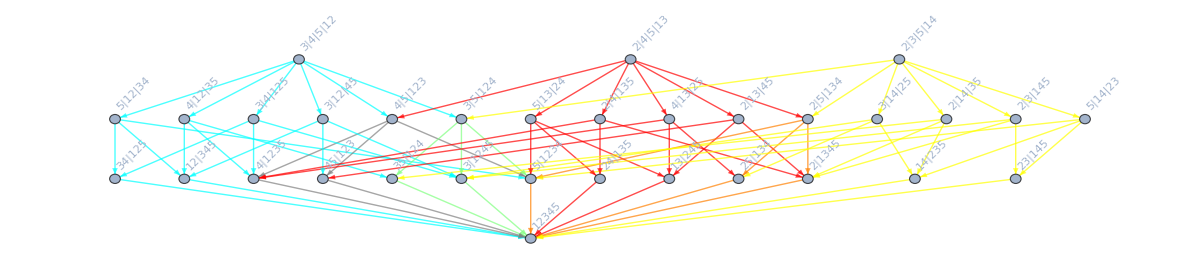

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->Rotate[SymbolToLabel[ SetsToSymbol[#]],Pi/4]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Cyan&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Yellow&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Mingle[Cyan,Red]&,Intersection[g1,g2]],
Map[#->Mingle[Cyan,Yellow]&,Intersection[g1,g3]],
Map[#->Mingle[Red,Yellow]&,Intersection[g2,g3]]
],
ImageSize->1200]
```

```mathematica
Table[StirlingS2[5,5-k],{k,0,5}]
```

{1,10,25,15,1,0}